ExampleCode for missing energy searches at e+e- colliders 
																				by Giovani Dalla Valle Garcia (KIT - DAAD)
											
Please don’t forget to cite https://arxiv.org/pdf/2405.08081 . 
If you use bounds from BaBar please cite https://arxiv.org/abs/1702.03327 . For Belle II sensitivities cite https://arxiv.org/abs/1808.10567 .

To get the bounds for BaBar/Belle II - sections and subsections names are in written between “quotes”:

run “Loading the package”
go to “Analysis via rescaling and not ab initio number of events”
run  “Basic geometrical and relativistic definitions”
go to “BaBar/Belle II”
run “Babar/Belle II rescaler”
go to “BaBar/Belle II Analysis”
do your work there ;)

If ComplexInfinity is returned as a bound for a given DM mass. It is probably because you are simulating too little events. Try increasing the number of events for this DM mass point. Also check if masses around it return finite values (if they do, just take the average for the problematic DM mass).

### Loading the package

```mathematica
SetDirectory[StringJoin[NotebookDirectory[],"PackageDirectory"](*directory where the eeCOLLIDERSeventGENERATORniDMv3 package is placed*)]
```

```mathematica
<<"eeCOLLIDERSeventGENERATORniDMv3`"
```

#### Check simulation is running

```mathematica
FullEventGenerator["e- e+ -> γ Z'",{0.25,3*0.25,0.1,3*10^-3,0,0.4},32.5,99,10.5641,{0,0,0.487603},3000,20000,20000,0];//AbsoluteTiming 
FullEventGenerator["e- e+ -> γ Z'",{0.25,3*0.25,0.1,3*10^-3,0,0.4},32.5,99,10.5641,{0,0,0.487603},3000,20000,20000,0];//AbsoluteTiming 
FullEventGenerator["e- e+ -> γ Z'",{0.25,3*0.25,0.1,3*10^-3,0,0.4},32.5,99,10.5641,{0,0,0.487603},3000,20000,20000,0];//AbsoluteTiming 
FullEventGenerator["e- e+ -> γ Z'",{0.25,3*0.25,0.1,3*10^-3,0,0.4},32.5,99,10.5641,{0,0,0.487603},3000,20000,20000,0];//AbsoluteTiming
```

Just a check. Give a look if things seem reasonable - you can just minimize this because it is not relevant since I believe everything should work.

```mathematica
SMEventsDisplay["e- e+ -> γ Z'",OnlySMEventSelected["e- e+ -> γ Z'",FullEventGenerator["e- e+ -> γ Z'",{0.25,3*0.25,0.1,3*10^-3,0,0.4},32.5,99,10.5641,{0,0,0.487603},3000,20000,20000,1],1][[1]],1]
```

```mathematica
MessageDialog[FullEventsDisplay["e- e+ -> γ Z'",FullEventGenerator["e- e+ -> γ Z'",{0.25,3*0.25,0.1,3*10^-3,0,0.4},32.5,99,10.5641,{0,0,0.487603},100,10000,10000,0][[1]],1,0],WindowTitle->"Zoom out to see it fully...",WindowSize->Full];
```

# Analysis via rescaling and not ab initio number of events

The rescaling functions you would probably use to generate your data are:

EpsBound[Parameters,minEps (*starting ϵ value*),epsIncrease,nEvents,nTrials,Verbose(*check each step*)] - which finds the value of the missing energy bound on the kinetic mixing ϵ by starting from an ϵ smaller than the bound itself and stepping up into larger ϵ until find the ϵ satisfying EpsBound[ϵ] = ϵ  .
*Parameters = {mDM,  mZp,  αD,  ϵ,   δy, Δm}
*the epsIncrease variable means that the next ϵ_next will be ϵ_next = epsIncrease*ϵ_old .
*nTrials is used to generate the random variables distribution - I suggest at least 2 times the number of events 

ReturnBounds[ZpFactor,alphaD,deltaY,DeltaM,mDMmin,mDMmax,nMassPoints,epsIncrease(*see above*),reduceFromPrevious,nEvents,nTrials] - scan over the dark matter mass for m_Z'=Zpfactor * m_χ finding the missing energy bound on the kinetic mixing ϵ .
*reduceFromPrevious is a trick to avoid starting all the way down from standard BaBar bounds in each m_DM step. Your initial minEps will be given now by minEps = reduceFromPrevious*EpsBound_previous . You just have to be careful to not kill any natural decrease of the bound, so I would suggest it to be: reduceFromPrevious < (3- 2epsIncrease). So you will at least decrease two steps of the size of your precision from the previous epsilon.

#### Basic geometrical and relativistic definitions

Boosts in every direction

```mathematica
EBoostedByV[Ener_,px_,py_,pz_,vx_,vy_,vz_]=Ener/Sqrt[1-vx^2-vy^2-vz^2]-(px*vx)/Sqrt[1-vx^2-vy^2-vz^2]-(py*vy)/Sqrt[1-vx^2-vy^2-vz^2]-(pz*vz)/Sqrt[1-vx^2-vy^2-vz^2];
PxBoostedByV[Ener_,px_,py_,pz_,vx_,vy_,vz_]=-((Ener*vx)/Sqrt[1-vx^2-vy^2-vz^2])+(py*vx*vy*(-1+1/Sqrt[1-vx^2-vy^2-vz^2]))/(vx^2+vy^2+vz^2)+(pz*vx*vz*(-1+1/Sqrt[1-vx^2-vy^2-vz^2]))/(vx^2+vy^2+vz^2)+px*(1+(vx^2*(-1+1/Sqrt[1-vx^2-vy^2-vz^2]))/(vx^2+vy^2+vz^2));
PyBoostedByV[Ener_,px_,py_,pz_,vx_,vy_,vz_]=-((Ener*vy)/Sqrt[1-vx^2-vy^2-vz^2])+(px*vx*vy*(-1+1/Sqrt[1-vx^2-vy^2-vz^2]))/(vx^2+vy^2+vz^2)+(pz*vy*vz*(-1+1/Sqrt[1-vx^2-vy^2-vz^2]))/(vx^2+vy^2+vz^2)+py*(1+(vy^2*(-1+1/Sqrt[1-vx^2-vy^2-vz^2]))/(vx^2+vy^2+vz^2));
PzBoostedByV[Ener_,px_,py_,pz_,vx_,vy_,vz_]=-((Ener*vz)/Sqrt[1-vx^2-vy^2-vz^2])+(px*vx*vz*(-1+1/Sqrt[1-vx^2-vy^2-vz^2]))/(vx^2+vy^2+vz^2)+(py*vy*vz*(-1+1/Sqrt[1-vx^2-vy^2-vz^2]))/(vx^2+vy^2+vz^2)+pz*(1+(vz^2*(-1+1/Sqrt[1-vx^2-vy^2-vz^2]))/(vx^2+vy^2+vz^2));
```

Defining a function for vectors for compactness

```mathematica
FourMomentumPrime[{E_,px_,py_,pz_},{vx_,vy_,vz_}]={EBoostedByV[E,px,py,pz,vx,vy,vz],PxBoostedByV[E,px,py,pz,vx,vy,vz],PyBoostedByV[E,px,py,pz,vx,vy,vz],PzBoostedByV[E,px,py,pz,vx,vy,vz]};
```

Angles with Z axis (usually beam axis)

```mathematica
θangleWithZaxis[{E_,px_,py_,pz_}]=ArcCos[pz/Norm[{px,py,pz}]];
θangleWithZaxis[{x_,y_,z_}]=ArcCos[z/Norm[{x,y,z}]];
θγCM[pγ_,velocityCM_]:=θangleWithZaxis[FourMomentumPrime[pγ,velocityCM]];
```

## BaBar

## Babar rescaler

### Defining the rescaler

#### Getting Babar reported missing energy bounds

```mathematica
SetDirectory[StringJoin[NotebookDirectory[],"PackageDirectory"](*directory where the input file is placed*)]
```

```mathematica
dataFromPaperBabar=Import["BaBarBounds.txt","Table"];(*https://arxiv.org/abs/1702.03327*)
```

```mathematica
ListLogLogPlot[dataFromPaperBabar,Joined->True]
BabarBounds=Interpolation[dataFromPaperBabar,InterpolationOrder->1];
```

#### BaBar experimental conditions

Following https://arxiv.org/pdf/1911.03176

```mathematica
(*angles in CM frame*)
EofCMBaBar=10.5641;
velocityCMBaBar={0,0,0.487603};
θγCMminBaBar=32.5;
θγCMmaxBaBar=99;
EγminBaBar=2;

(*angles in lab frame*)
θminBaBarCal=17(*degrees*);
θmaxBaBarCal=142(*degrees*);
θminBaBarMuS=20(*degrees*);
θmaxBaBarMuS=150(*degrees*);
EeminBaBarCal=0.15(*GeV*);
PeminBaBarCal=0.15(*GeV*);
EeminBaBarMuS=0.3(*GeV*);
PeminBaBarMuS=0.3(*GeV*);
ZeminBaBarCal=-1.13(*m*);
ZemaxBaBarCal=1.85(*m*);
ZeminBaBarMuS=-2.23(*m*);
ZemaxBaBarMuS=2.97(*m*);
RxyemaxBaBarCal=1.02(*m*);
RxyemaxBaBarMuS=2.43(*m*);
```

#### Particle selection cuts

Photon selection

```mathematica
(*PhotonCut[{pγ_,pZp_}]:=(θγCMmax*π/180>θγCM[pγ,velocityCMBaBar]>θγCMmin*π/180)&&(pγ[[1]]>Eγmin);*)
```

```mathematica
(*actually we can generate events already within the photon angular selection*)
```

```mathematica
PhotonCut[{γ_,vertex1SMinfo_,vertex2SMinfo_}]:=γ[[2]][[1]]>EγminBaBar;
```

Charged particles selection

```mathematica
ChargedParticle[{γ_,vertex1SMinfo_,vertex2SMinfo_}]:=If[vertex1SMinfo===Null,False,((*BEGIN calorimeter cuts*)((*BEGIN vertex position cuts*)(ZeminBaBarCal<vertex1SMinfo[[1]][[3]]<ZemaxBaBarCal)&&(Norm[vertex1SMinfo[[1]][[1;;2]]]<RxyemaxBaBarCal)&&(θmaxBaBarCal*π/180>θangleWithZaxis[vertex1SMinfo[[1]] ]>θminBaBarCal*π/180)(*END vertex position cuts*))&&((*BEGIN particles cuts*)((*BEGIN particle1 cuts*)If[vertex1SMinfo[[2]][[1]]==="e^-", (vertex1SMinfo[[2]][[2]][[1]]>EeminBaBarCal),(Norm[vertex1SMinfo[[2]][[2]][[2;;4]]]>PeminBaBarCal)](*END particle1 cuts*))||((*BEGIN particle2 cuts*) If[vertex1SMinfo[[3]][[1]]==="e^+", (vertex1SMinfo[[3]][[2]][[1]]>EeminBaBarCal),(Norm[vertex1SMinfo[[3]][[2]][[2;;4]]]>PeminBaBarCal)](*END particle2 cuts*))(*END particles cuts*))(*END calorimeter cuts*))||((*BEGIN muon system cuts*)((*BEGIN vertex position cuts*)(ZeminBaBarMuS<vertex1SMinfo[[1]][[3]]<ZemaxBaBarMuS)&&(Norm[vertex1SMinfo[[1]][[1;;2]]]<RxyemaxBaBarMuS)&&(θmaxBaBarMuS*π/180>θangleWithZaxis[vertex1SMinfo[[1]]]>θminBaBarMuS*π/180)(*END vertex position cuts*))&&((*BEGIN particle cuts*)If[vertex1SMinfo[[2]][[1]]==="e^-", ((vertex1SMinfo[[2]][[2]][[1]]+vertex1SMinfo[[3]][[2]][[1]])>EeminBaBarMuS),((Norm[vertex1SMinfo[[2]][[2]][[2;;4]]]+Norm[vertex1SMinfo[[3]][[2]][[2;;4]]])>PeminBaBarMuS)] (*END particle cuts*))(*END muon system cuts*))]||If[vertex2SMinfo===Null,False,((*BEGIN calorimeter cuts*)((*BEGIN vertex position cuts*)(ZeminBaBarCal<vertex2SMinfo[[1]][[3]]<ZemaxBaBarCal)&&(Norm[vertex2SMinfo[[1]][[1;;2]]]<RxyemaxBaBarCal)&&(θmaxBaBarCal*π/180>θangleWithZaxis[vertex2SMinfo[[1]] ]>θminBaBarCal*π/180)(*END vertex position cuts*))&&((*BEGIN particles cuts*)((*BEGIN particle1 cuts*)If[vertex2SMinfo[[2]][[1]]==="e^-", (vertex2SMinfo[[2]][[2]][[1]]>EeminBaBarCal),(Norm[vertex2SMinfo[[2]][[2]][[2;;4]]]>PeminBaBarCal)](*END particle1 cuts*))||((*BEGIN particle2 cuts*) If[vertex2SMinfo[[3]][[1]]==="e^+", (vertex2SMinfo[[3]][[2]][[1]]>EeminBaBarCal),(Norm[vertex2SMinfo[[3]][[2]][[2;;4]]]>PeminBaBarCal)](*END particle2 cuts*))(*END particles cuts*))(*END calorimeter cuts*))||((*BEGIN muon system cuts*)((*BEGIN vertex position cuts*)(ZeminBaBarMuS<vertex2SMinfo[[1]][[3]]<ZemaxBaBarMuS)&&(Norm[vertex2SMinfo[[1]][[1;;2]]]<RxyemaxBaBarMuS)&&(θmaxBaBarMuS*π/180>θangleWithZaxis[vertex2SMinfo[[1]]]>θminBaBarMuS*π/180)(*END vertex position cuts*))&&((*BEGIN particle cuts*)If[vertex2SMinfo[[2]][[1]]==="e^-", ((vertex2SMinfo[[2]][[2]][[1]]+vertex2SMinfo[[3]][[2]][[1]])>EeminBaBarMuS),((Norm[vertex2SMinfo[[2]][[2]][[2;;4]]]+Norm[vertex2SMinfo[[3]][[2]][[2;;4]]])>PeminBaBarMuS)] (*END particle cuts*))(*END muon system cuts*))];
```

#### Definitions for rescaling

Function which tells how likely the SM particles produced in association with the photon are to be detected.

```mathematica
EventDetectabilityProb[Parameters_,nEvents_,nTrialsPhoton_,nTrialsChi_]:=Module[{AllEvents,EventsAfterElecPosSelection},
AllEvents=OnlySMEventSelected["e- e+ -> γ Z'",FullEventGenerator["e- e+ -> γ Z'",Parameters,θγCMminBaBar,θγCMmaxBaBar,EofCMBaBar,velocityCMBaBar,nEvents,nTrialsPhoton,nTrialsChi,0],0];(*already satisfying photon cuts because we choose the angles and min E is always larger than 2 GeV (we verified it), so AllEvents = EventsAfterPhotonCut in our case*);

EventsAfterElecPosSelection=Select[Select[AllEvents ,PhotonCut] ,ChargedParticle];

(EventsAfterElecPosSelection//Length)/(AllEvents//Length)
]
```

Function which starts at the lowest epsilon and computes the scaled bound until find a point where Bound[ϵ]=ϵ .

```mathematica
EpsBound[Parameters_,minEps_,epsStepSize_,nEvents_,nTrials_,Verbose_]:=Module[{CurrentEps,CurrentEpsBound,mZp,CurrentParameters,i},
CurrentEps=minEps;
CurrentParameters={Parameters[[1]],Parameters[[2]],Parameters[[3]],CurrentEps,Parameters[[5]],Parameters[[6]]};
mZp=Parameters[[2]];

If[mZp>0.999*dataFromPaperBabar[[-1]][[1]](*above BaBar bounds*),1,CurrentEpsBound=Mean[Table[BabarBounds[mZp]/(√(1-EventDetectabilityProb[CurrentParameters,nEvents,nTrials,nTrials])),3]];

If[Verbose===1,i=1;Print["Step " , i, ":"];Print["eps = " , CurrentEps, " and bound = ", CurrentEpsBound];,0;];

While[CurrentEps<CurrentEpsBound&&CurrentEps<3*10^-2,
CurrentEps=epsStepSize*CurrentEps;
CurrentParameters={Parameters[[1]],Parameters[[2]],Parameters[[3]],CurrentEps,Parameters[[5]],Parameters[[6]]};
CurrentEpsBound=Mean[Table[BabarBounds[mZp]/(√(1-EventDetectabilityProb[CurrentParameters,nEvents,nTrials,nTrials])),2]];

If[Verbose===1,i=i+1;Print["Step " , i, ":"];Print["eps = " , CurrentEps, " and bound = ", CurrentEpsBound];,0;];

];

(* taking the value from half a step once we have stopped*)
CurrentEps=CurrentEps/(√epsStepSize) ;
CurrentParameters={Parameters[[1]],Parameters[[2]],Parameters[[3]],CurrentEps,Parameters[[5]],Parameters[[6]]};
CurrentEpsBound=Mean[Table[BabarBounds[mZp]/(√(1-EventDetectabilityProb[CurrentParameters,nEvents,nTrials,nTrials])),3]];

If[Verbose===1,Print["Final Step:"];Print["eps = " , CurrentEps, " and bound = ", CurrentEpsBound];,0;];

CurrentEpsBound

]


]
```

#### Definition of mass scanner - useful to reproduce the usual plots in m_χ x ϵ

Function which run over the dark matter masses (and the dark photon as well, since we define it to be proportional to the dark matter mass m_Z'=Zpfactor * m_χ) finding the corresponding new kinetic mixing bounds from missing energy searches. The function automatically export the results into a file.

```mathematica
ReturnBounds[ZpFactor_,alphaD_,deltaY_,DeltaM_,mDMmin_,mDMmax_,nPoints_,epsStepSize_,reduceFromPrevious_,nEvents_,nTrials_]:=Module[{BSMmodelInputsList,mDMtemp,j,previousBound,epsBounds},

BSMmodelInputsList=Table[{(mDMtemp=mDMmin(mDMmax/mDMmin)^(j/(nPoints-1))),ZpFactor*mDMtemp,alphaD,reduceFromPrevious*BabarBounds[0.05](*any value*),deltaY,DeltaM} (*{mDM,  mZp,  αD,  ϵ,   δy, Δf}*),{j,0,nPoints-1}];

previousBound=0.9*BabarBounds[0.05];
j=0;

epsBounds=Monitor[Table[{BSMmodelInputsList[[(j=i)]][[1]],(previousBound=EpsBound[BSMmodelInputsList[[i]],reduceFromPrevious*Max[previousBound,BabarBounds[BSMmodelInputsList[[i]][[2]]]],epsStepSize,nEvents,nTrials,0])},{i,1,nPoints}],{j,ProgressIndicator[(j-1)/nPoints+0.75/nPoints]}];

SetDirectory[NotebookDirectory[]];

Print[Export[StringJoin["Output\\epsResultsZpFac",ToString[ZpFactor],"alphaD",ToString[alphaD],"deltaY",ToString[deltaY],"DeltaM",ToString[DeltaM],"BaBar.dat"],epsBounds,"Table"]];

epsBounds
]
```

### Testing the rescaling

```mathematica
test1=Quiet[ReturnBounds[3,0.1,0,0.4,0.02,2.3,4,1.15,0.8,750,2000]];//AbsoluteTiming
```

```mathematica
SetDirectory[StringJoin[NotebookDirectory[],"PackageDirectory"](*directory where the input file is placed*)]
dataFromPaper1=Import["dataFIG5bottomRIGHT.csv","Dataset"]; (*https://arxiv.org/pdf/1911.03176*)
```

```mathematica
MessageDialog[ListLogLogPlot[{dataFromPaper1,test1,Table[{(dataFromPaperBabar[[i]][[1]])/3,dataFromPaperBabar[[i]][[2]]},{i,1,dataFromPaperBabar//Length}]},PlotStyle->{Black,Blue,{LightGray,Dashed}},Joined->{True,False,True},PlotLegends->{"1911.03176","this work","original BaBar"},PlotMarkers->{None,"\!\(\*
StyleBox[\"☺\",\nFontSize->18]\)",None},AxesLabel->{"m_χ","ϵ"},PlotLabel->"m_Z'=3m_χ , α'=0.1 , Δ_m=0.4 , δ_y=0",PlotRange->{{0.01,10},Automatic}],WindowTitle->"BaBar missing energy searches",WindowSize->{500,300}];(*presenting you the results of the comparison*)
```

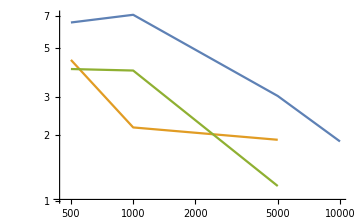
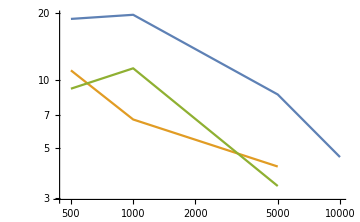
standard deviation in the ϵ bound prediction  X simulated number of events                    maximum variation (statistical error) in the ϵ bound prediction  X simulated number of events          
-Graphics-                                                 -Graphics-

The green line is the most relevant which is the actual EpsBound used in this notebook. Looking at the plot, I would suggest to simulate more than a 1000 events and always at least double the number of points for the random generator, i.e., the input variable nTrials >= 2 nEvents.

## BaBar Analysis

Do your analysis here. You will probably only use the code below (check the sub section “Testing the rescaling” to see an example):

```mathematica
mZpFactorPlot=2.5;alphaDplot=0.1;deltaYplot=0.1;DeltaMplot=0.4;
mDMmixPlot=0.009;mDMmaxPlot=12;mDMstepsPlot=6;
epsIncreasePlot=1.15;reduceFromPreviousPlot=0.8;nEvents=500;nTrials=1000;

dataBaBarBounds=Quiet[ReturnBounds[mZpFactorPlot,alphaDplot,deltaYplot,DeltaMplot,mDMmixPlot,mDMmaxPlot,mDMstepsPlot,epsIncreasePlot,reduceFromPreviousPlot,nEvents,nTrials]];
```

```mathematica
ListLogLogPlot[dataBaBarBounds,Joined->True]
```

Recommendations: 
epsIncrease=1.03, reduceFromPrevious=0.94, nEvents=2500, nTrials=5000 for mDM in (0.01 GeV,10 GeV) and mDMstepsPlot = 100.
But of course more accuracy is always okay if you have time to let your computer running longer. 

I also suggest breaking the ReturnBounds into pieces so you save data partially and do not lose everything in case of an error.

## Belle II

## Belle II rescaler

### Defining the rescaler

#### Getting Belle II reported missing energy bounds

```mathematica
SetDirectory[StringJoin[NotebookDirectory[],"PackageDirectory"](*directory where the input file is placed*)]
```

```mathematica
dataFromPaperBelleII=Import["BelleIIbounds.csv","Data"];(*https://arxiv.org/abs/1808.10567*)
```

```mathematica
ListLogLogPlot[dataFromPaperBelleII,Joined->True]
BelleIIBounds=Interpolation[dataFromPaperBelleII,InterpolationOrder->1];
```

#### Belle II experimental conditions

Following https://arxiv.org/pdf/1911.03176

```mathematica
(*angles in CM frame*)
velocityCMBelleII={0,0.041488,0.272525};
EofCMBelleII=10.5796;
θγCMminBelleII=23;
θγCMmaxBelleII=138;
θγCMminBelleIISelection[Eγ_,mZp_]:=Piecewise[{{5.399*Eγ^2-58.82*Eγ+195.71,mZp<6},{3.3133*Eγ^2-33.58*Eγ+108.79,mZp>=6}}];
θγCMmaxBelleIISelection[Eγ_,mZp_]:=Piecewise[{{-7.982*Eγ^2+87.77*Eγ-120.6,mZp<6},{-5.9133*Eγ^2+54.119*Eγ+13.781,mZp>=6}}];
EγminBelleII=2;

(*angles in lab frame*)
θminBelleIICal=17(*degrees*);
θmaxBelleIICal=150(*degrees*);
θminBelleIIMuS=25(*degrees*);
θmaxBelleIIMuS=145(*degrees*);
EeminBelleIICal=0.15(*GeV*);
PeminBelleIICal=0.15(*GeV*);
EeminBelleIIMuS=0.3(*GeV*);
PeminBelleIIMuS=0.3(*GeV*);
ZeminBelleIICal=-1.12(*m*);
ZemaxBelleIICal=2.06(*m*);
ZeminBelleIIMuS=-3(*m*);
ZemaxBelleIIMuS=4(*m*);
RxyemaxBelleIICal=1.35(*m*);
RxyemaxBelleIIMuS=3(*m*);
```

#### Particle selection cuts

Photon selection

```mathematica
PhotonCut1[{{γ_,pγ_},vertex1SMinfo_,vertex2SMinfo_}]:=(θγCMmaxBelleIISelection[pγ[[1]],1]*π/180>θγCM[pγ,velocityCMBelleII]>θγCMminBelleIISelection[pγ[[1]],1]*π/180)&&(pγ[[1]]>EγminBelleII);
PhotonCut10[{{γ_,pγ_},vertex1SMinfo_,vertex2SMinfo_}]:=(θγCMmaxBelleIISelection[pγ[[1]],10]*π/180>θγCM[pγ,velocityCMBelleII]>θγCMminBelleIISelection[pγ[[1]],10]*π/180)&&(pγ[[1]]>EγminBelleII);
```

Charged particle selection

```mathematica
ChargedParticle[{γ_,vertex1SMinfo_,vertex2SMinfo_}]:=If[vertex1SMinfo===Null,False,((*BEGIN calorimeter cuts*)((*BEGIN vertex position cuts*)(ZeminBelleIICal<vertex1SMinfo[[1]][[3]]<ZemaxBelleIICal)&&(Norm[vertex1SMinfo[[1]][[1;;2]]]<RxyemaxBelleIICal)&&(θmaxBelleIICal*π/180>θangleWithZaxis[vertex1SMinfo[[1]] ]>θminBelleIICal*π/180)(*END vertex position cuts*))&&((*BEGIN particles cuts*)((*BEGIN particle1 cuts*)If[vertex1SMinfo[[2]][[1]]==="e^-", (vertex1SMinfo[[2]][[2]][[1]]>EeminBelleIICal),(Norm[vertex1SMinfo[[2]][[2]][[2;;4]]]>PeminBelleIICal)](*END particle1 cuts*))||((*BEGIN particle2 cuts*) If[vertex1SMinfo[[3]][[1]]==="e^+", (vertex1SMinfo[[3]][[2]][[1]]>EeminBelleIICal),(Norm[vertex1SMinfo[[3]][[2]][[2;;4]]]>PeminBelleIICal)](*END particle2 cuts*))(*END particles cuts*))(*END calorimeter cuts*))||((*BEGIN muon system cuts*)((*BEGIN vertex position cuts*)(ZeminBelleIIMuS<vertex1SMinfo[[1]][[3]]<ZemaxBelleIIMuS)&&(Norm[vertex1SMinfo[[1]][[1;;2]]]<RxyemaxBelleIIMuS)&&(θmaxBelleIIMuS*π/180>θangleWithZaxis[vertex1SMinfo[[1]]]>θminBelleIIMuS*π/180)(*END vertex position cuts*))&&((*BEGIN particle cuts*)If[vertex1SMinfo[[2]][[1]]==="e^-", ((vertex1SMinfo[[2]][[2]][[1]]+vertex1SMinfo[[3]][[2]][[1]])>EeminBelleIIMuS),((Norm[vertex1SMinfo[[2]][[2]][[2;;4]]]+Norm[vertex1SMinfo[[3]][[2]][[2;;4]]])>PeminBelleIIMuS)] (*END particle cuts*))(*END muon system cuts*))]||If[vertex2SMinfo===Null,False,((*BEGIN calorimeter cuts*)((*BEGIN vertex position cuts*)(ZeminBelleIICal<vertex2SMinfo[[1]][[3]]<ZemaxBelleIICal)&&(Norm[vertex2SMinfo[[1]][[1;;2]]]<RxyemaxBelleIICal)&&(θmaxBelleIICal*π/180>θangleWithZaxis[vertex2SMinfo[[1]] ]>θminBelleIICal*π/180)(*END vertex position cuts*))&&((*BEGIN particles cuts*)((*BEGIN particle1 cuts*)If[vertex2SMinfo[[2]][[1]]==="e^-", (vertex2SMinfo[[2]][[2]][[1]]>EeminBelleIICal),(Norm[vertex2SMinfo[[2]][[2]][[2;;4]]]>PeminBelleIICal)](*END particle1 cuts*))||((*BEGIN particle2 cuts*) If[vertex2SMinfo[[3]][[1]]==="e^+", (vertex2SMinfo[[3]][[2]][[1]]>EeminBelleIICal),(Norm[vertex2SMinfo[[3]][[2]][[2;;4]]]>PeminBelleIICal)](*END particle2 cuts*))(*END particles cuts*))(*END calorimeter cuts*))||((*BEGIN muon system cuts*)((*BEGIN vertex position cuts*)(ZeminBelleIIMuS<vertex2SMinfo[[1]][[3]]<ZemaxBelleIIMuS)&&(Norm[vertex2SMinfo[[1]][[1;;2]]]<RxyemaxBelleIIMuS)&&(θmaxBelleIIMuS*π/180>θangleWithZaxis[vertex2SMinfo[[1]]]>θminBelleIIMuS*π/180)(*END vertex position cuts*))&&((*BEGIN particle cuts*)If[vertex2SMinfo[[2]][[1]]==="e^-", ((vertex2SMinfo[[2]][[2]][[1]]+vertex2SMinfo[[3]][[2]][[1]])>EeminBelleIIMuS),((Norm[vertex2SMinfo[[2]][[2]][[2;;4]]]+Norm[vertex2SMinfo[[3]][[2]][[2;;4]]])>PeminBelleIIMuS)] (*END particle cuts*))(*END muon system cuts*))];
```

#### Definitions for rescaling

Function which tells how likely the SM particles produced in association with the photon are to be detected.

```mathematica
EventDetectabilityProb[Parameters_,nEvents_,nTrialsPhoton_,nTrialsChi_]:=Module[{AllEvents,EventsAfterElecPosSelection,EventsAfterPhotonSelection},
AllEvents=OnlySMEventSelected["e- e+ -> γ Z'",FullEventGenerator["e- e+ -> γ Z'",Parameters,θγCMminBelleII,θγCMmaxBelleII,EofCMBelleII,velocityCMBelleII,nEvents,nTrialsPhoton,nTrialsChi,0],0];

If[Parameters[[2]]<6(*mZp lighter than 6 GeV*),EventsAfterPhotonSelection=Select[AllEvents ,PhotonCut1] ;,EventsAfterPhotonSelection=Select[AllEvents ,PhotonCut10] ;];

EventsAfterElecPosSelection=Select[EventsAfterPhotonSelection ,ChargedParticle];

If[(EventsAfterPhotonSelection//Length)===0,Print["Error: no mono-photon event detected (out of ",AllEvents//Length , " events generated)"];0,(EventsAfterElecPosSelection//Length)/(EventsAfterPhotonSelection//Length)]
]
```

Function which starts at the lowest epsilon and computes the scaled bound until find a point where Bound[ϵ]=ϵ .

```mathematica
EpsBound[Parameters_,minEps_,epsStepSize_,nEvents_,nTrials_,Verbose_]:=Module[{CurrentEps,CurrentEpsBound,mZp,CurrentParameters,i},
CurrentEps=minEps;
CurrentParameters={Parameters[[1]],Parameters[[2]],Parameters[[3]],CurrentEps,Parameters[[5]],Parameters[[6]]};
mZp=Parameters[[2]];

If[mZp>0.999*dataFromPaperBelleII[[-1]][[1]](*above Belle II bounds*),1,CurrentEpsBound=Mean[Table[BelleIIBounds[mZp]/(√(1-EventDetectabilityProb[CurrentParameters,nEvents,nTrials,nTrials])),3]];

If[Verbose===1,i=1;Print["Step " , i, ":"];Print["eps = " , CurrentEps, " and bound = ", CurrentEpsBound];,0;];

While[CurrentEps<CurrentEpsBound&&CurrentEps<3*10^-2,
CurrentEps=CurrentEps*epsStepSize;
CurrentParameters={Parameters[[1]],Parameters[[2]],Parameters[[3]],CurrentEps,Parameters[[5]],Parameters[[6]]};
CurrentEpsBound=Mean[Table[BelleIIBounds[mZp]/(√(1-EventDetectabilityProb[CurrentParameters,nEvents,nTrials,nTrials])),2]];

If[Verbose===1,i=i+1;Print["Step " , i, ":"];Print["eps = " , CurrentEps, " and bound = ", CurrentEpsBound];,0;];

];

(* taking the value from half a step once we have stopped*)
CurrentEps=CurrentEps/(√epsStepSize);
CurrentParameters={Parameters[[1]],Parameters[[2]],Parameters[[3]],CurrentEps,Parameters[[5]],Parameters[[6]]};
CurrentEpsBound=Mean[Table[BelleIIBounds[mZp]/(√(1-EventDetectabilityProb[CurrentParameters,nEvents,nTrials,nTrials])),3]];

If[Verbose===1,Print["Final Step:"];Print["eps = " , CurrentEps, " and bound = ", CurrentEpsBound];,0;];

CurrentEpsBound

]


]
```

#### Definition of mass scanner - useful to reproduce the usual plots in m_χ x ϵ

Function which run over the dark matter masses (and the dark photon as well, since we define it to be proportional to the dark matter mass m_Z'=Zpfactor * m_χ) finding the corresponding new kinetic mixing bounds from missing energy searches. The function automatically export the results into a file.

```mathematica
ReturnBounds[ZpFactor_,alphaD_,deltaY_,DeltaM_,mDMmin_,mDMmax_,nPoints_,epsStepSize_,reduceFromPrevious_,nEvents_,nTrials_]:=Module[{BSMmodelInputsList,mDMtemp,j,previousBound,epsBounds},

BSMmodelInputsList=Table[{(mDMtemp=mDMmin(mDMmax/mDMmin)^(j/(nPoints-1))),ZpFactor*mDMtemp,alphaD,0.5*reduceFromPrevious*BelleIIBounds[0.05](*any value*),deltaY,DeltaM} (*{mDM,  mZp,  αD,  ϵ,   δy, Δf}*),{j,0,nPoints-1}];

previousBound=0.5*BelleIIBounds[0.03];
j=0;

epsBounds=Monitor[Table[{BSMmodelInputsList[[(j=i)]][[1]],(previousBound=EpsBound[BSMmodelInputsList[[i]],reduceFromPrevious*Max[previousBound,BelleIIBounds[BSMmodelInputsList[[i]][[2]]]],epsStepSize,nEvents,nTrials,0])},{i,1,nPoints}],{j,ProgressIndicator[(j-1)/nPoints+0.75/nPoints]}];

SetDirectory[NotebookDirectory[]];

Print[Export[StringJoin["Output\\epsResultsZpFac",ToString[ZpFactor],"alphaD",ToString[alphaD],"deltaY",ToString[deltaY],"DeltaM",ToString[DeltaM],"BelleII.dat"],epsBounds,"Table"]];

epsBounds
]
```

### Testing the rescaling

```mathematica
test2=Quiet[ReturnBounds[3,0.1,0,0.4,0.02,2,4,1.40,0.75,750,2000]];//AbsoluteTiming
```

```mathematica
SetDirectory[StringJoin[NotebookDirectory[],"PackageDirectory"](*directory where the input file is placed*)]
dataFromPaper2=Import["dataFIG5bottomRIGHTbelle.csv","Dataset"];(*https://arxiv.org/pdf/1911.03176*)
```

```mathematica
MessageDialog[ListLogLogPlot[{dataFromPaper2,test2,Table[{(dataFromPaperBelleII[[i]][[1]])/3,dataFromPaperBelleII[[i]][[2]]},{i,1,dataFromPaperBelleII//Length}]},PlotStyle->{Black,Red,{LightGray,Dashed}},Joined->{True,False,True},PlotLegends->{"1911.03176","this work","original Belle II"},PlotMarkers->{None,"\!\(\*
StyleBox[\"☺\",\nFontSize->18]\)",None},AxesLabel->{"m_χ","ϵ"},PlotLabel->"m_Z'=3m_χ , α'=0.1 , Δ_m=0.4 , δ_y=0",PlotRange->{{0.01,10},Automatic}],WindowTitle->"Belle II missing energy searches",WindowSize->{500,300}];
```

standard deviation in the ϵ bound prediction  X simulated number of events                    maximum variation (statistical error) in the ϵ bound prediction  X simulated number of events          
-Graphics-                                                 -Graphics-

The green line is the most relevant which is the actual EpsBound used in this notebook. Looking at the plot, I would suggest to simulate more than a 1000 events and always at least double the number of points for the random generator, i.e., the input variable nTrials >= 2 nEvents.

## Belle II Analysis

Do your analysis here. You will probably only use the code below (check the sub section “Testing the rescaling” to see an example):

```mathematica
mZpFactorPlot=2.5;alphaDplot=0.1;deltaYplot=0.1;DeltaMplot=0.4;
mDMmixPlot=0.009;mDMmaxPlot=11;mDMstepsPlot=6;
epsIncreasePlot=1.15;reduceFromPreviousPlot=0.8;nEvents=500;nTrials=1000;

dataBelleIIBounds=Quiet[ReturnBounds[mZpFactorPlot,alphaDplot,deltaYplot,DeltaMplot,mDMmixPlot,mDMmaxPlot,mDMstepsPlot,epsIncreasePlot,reduceFromPreviousPlot,nEvents,nTrials]];//AbsoluteTiming
```

```mathematica
ListLogLogPlot[dataBelleIIBounds,Joined->True]
```

Recommendations: 
epsIncrease=1.03, reduceFromPrevious=0.94, nEvents=2500, nTrials=5000 for mDM in (0.01 GeV,10 GeV) and mDMstepsPlot = 100.
But of course more accuracy is always okay if you have time to let your computer running longer. 

I also suggest breaking the ReturnBounds into pieces so you save data partially and do not lose everything in case of an error.